```mathematica
SetDirectory["\\\\apclara1\\jkj62\\OnlineModel\\FrameworkTest\\Examples\\transverse_DCP_best_Short_240"]
```

\\apclara1\jkj62\OnlineModel\FrameworkTest\Examples\transverse_DCP_best_Short_240

```mathematica
Import["./CLA-S07-DCP-01-SCR.hdf5","/beam/columns"]
```

{x,y,z,cpx,cpy,cpz,t,q}

```mathematica
{x,y,z,cpx,cpy,cpz,t,q}=Transpose[Import["./CLA-S07-DCP-01-SCR.hdf5","/beam/beam"]];
```

```mathematica
lplot=ListPlot[{10^6 Transpose[{x,y}]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

-Graphics-

```mathematica
z[[1]]
```

43.9309

```mathematica
Transpose[{z,cpz}][[2]]
```

{43.9309,2.49073×10^8}

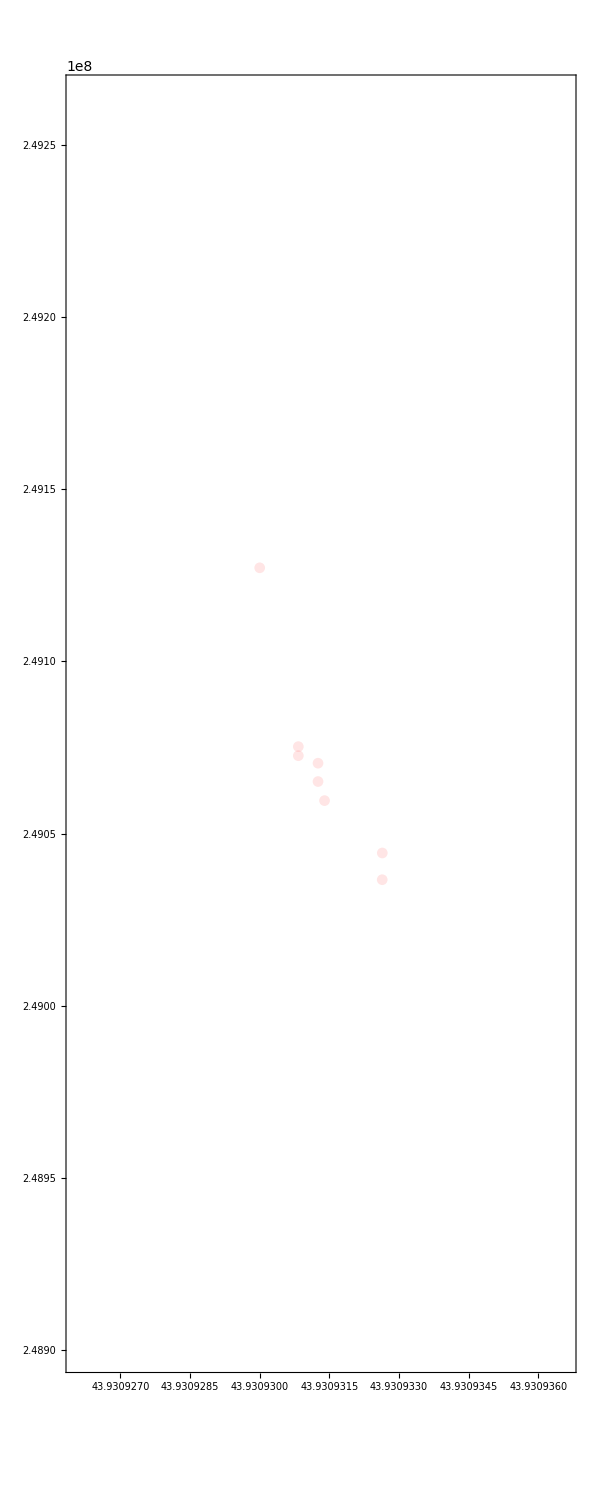

```mathematica
lplot=ListPlot[{Transpose[{z,cpz}][[1;;10]]},AspectRatio->Automatic,Frame->True,ImageSize->600,PlotStyle->{{Red,Opacity[0.1]}}]
```

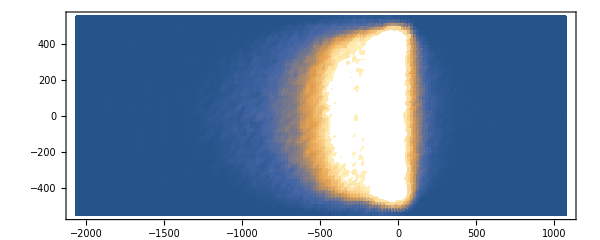

```mathematica
dplot=ListDensityPlot[Transpose[BinCounts[10^6 Transpose[{x,y}],20,20]],AspectRatio->Automatic,ImageSize->600,DataRange->{10^6{Min[x],Max[x]},10^6{Min[y],Max[y]}}]
```

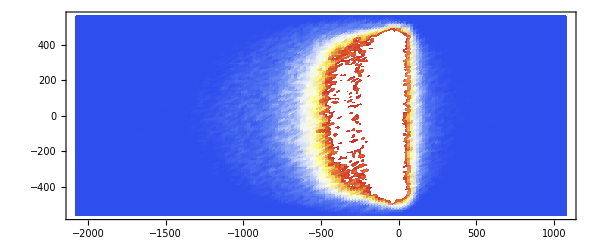

```mathematica
dplot=Block[{bins,hdata},
{bins,hdata}=HistogramList[10^6 Transpose[{x,y}],{100,100}];
ListDensityPlot[Transpose[hdata],AspectRatio->Automatic,ImageSize->600,DataRange->({#[[1]],#[[-1]]}&/@bins),Mesh->None,ColorFunction->(ColorData["TemperatureMap"])]]
```